```mathematica
(* Explain the meaning of each line *)
```

```mathematica
(*Subscript[x, n] is drawn from a uniform distribution in [0,1]*)
x[n_] := RandomReal[]
```

```mathematica
(*Subscript[x, 1]*)
x[1]
```

0.289361

```mathematica
(*Subscript[x, 2]*)
x[2]
```

0.839529

```mathematica
(*Average of Subscript[x, 1], Subscript[x, 2], Subscript[x, 3]... upto Subscript[x, n], in the limit n->∞, the distribution of this average approaches to a gaussian with 0 standard deviation, which is a dirac delta distribution*)
AvgX[n_] := Sum[x[j],{j,1,n}]/n
(*Average of Subscript[x, 1], Subscript[x, 2], Subscript[x, 3]... upto Subscript[x, n], subtracted from mean of the uniform distribution, scaled by √n. This is the random variate appearing in the Central Limit Theorem, its distribution approaches towards a Gaussian with finite standard deviation*)
CLTX[n_]:=(Sum[x[j],{j,1,n}]/n-0.5)√n
```

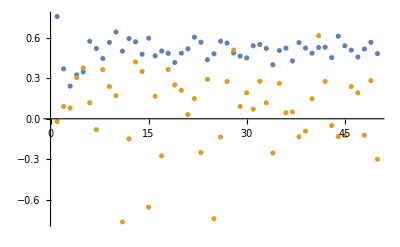

```mathematica
(*As we can indeed see, the distribution of the average is being squished for large n but the random variate appearing in CLT has an almost constant σ*)
ListPlot[ {Table[AvgX[n],{n,1,50}],Table[CLTX[n],{n,1,50}]}]
```

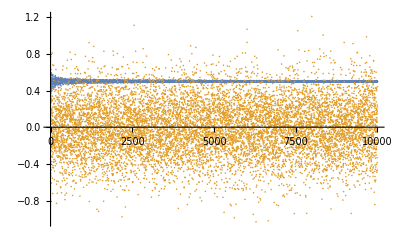

```mathematica
(*As we can indeed see, the distribution of the average is being squished for large n(approaching a δ distribution) but the random variate appearing in CLT is a Gaussian with almost constant σ*)
ListPlot[ {Table[AvgX[n],{n,1,10^4}],Table[CLTX[n],{n,1,10^4}]}]
```

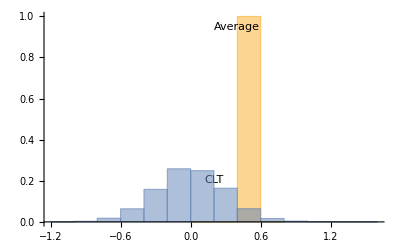

```mathematica
(*A better representation is the histogram, where we can see the distributions*) 
Histogram[{Table[AvgX[n],{n,1,10^4}],Table[CLTX[n],{n,1,10^4}]},Automatic,"Probability",ChartLabels->{"Average","CLT"}]
```